## Set Directories

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-10-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolder,dataFolder}];
SetDirectory[folder];
FileNames[]

SetDirectory[FileNameJoin[{folder,"17-11-15_BalancedPhotoDetector"}]];
(*names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];*)
names=FileNames[]
```

## Functions

### Mueller Matrix

#### According to a Chp 22 in an optics handbook (chapter authored by Russell A. Chipman), We have the following mueller matrix for a general retarder

```mathematica
(* The retardance is entered as a fraction. For example, a half-wave plate will be enterered as 1/2 *)
LR[θfast_,retardance_]:=({{1, 0, 0, 0}, {0, Cos[2θfast]^2+Sin[2θfast]^2Cos[2π retardance], Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), -Sin[2θfast]Sin[2π retardance]}, {0, Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), Sin[2θfast]^2+Cos[2θfast]Cos[2π retardance]^2, Cos[2 θfast]Sin[2π retardance]}, {0, Sin[2θfast]Sin[2π retardance], -Cos[2 θfast]Sin[2π retardance], Cos[2π retardance]}})
LRzero[δ_]:=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[δ], Sin[δ]}, {0, 0, -Sin[δ], Cos[δ]}});
LPzero=1/2({{1, 1, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
MuellerRotation[θ_]:=({{1, 0, 0, 0}, {0, Cos[2θ], -Sin[2θ], 0}, {0, Sin[2θ], Cos[2θ], 0}, {0, 0, 0, 1}})
```

### Discreet Fourier Transform

```mathematica
(* Discreet Fourier Transform for the Cos Function *)
```

```mathematica
DFTC[list_,rev_]:=Module[{numItems,i,k,j,returnList,intensity},
returnList={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnList,0];
];

For[k=1,k<=numItems,k++,
intensity=list[[k]];
For [i=0,i<numItems/2,i++,
If[i==0 ||i==(numItems/2-1),
returnList[[i+1]]=returnList[[i+1]]+1/numItems*intensity*Cos[2*π *i *rev* (k-1)/numItems];,
returnList[[i+1]]=returnList[[i+1]]+2/numItems*intensity*Cos[2*π *i* rev *(k-1)/numItems];
];
];
];

returnList
];
(* Discreet Fourier Transform for the Sin Function *)
DFTS[list_,rev_]:=Module[{numItems,i,k,j,error,returnList,intensity,errors},
returnList={};
error={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnList,0];
AppendTo[errors,0];
];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnList[[k+1]]=returnList[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems];,
returnList[[k+1]]=returnList[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems];
];
];
];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnList[[k+1]]=returnList[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems];,
returnList[[k+1]]=returnList[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems];
];
];
];

returnList
];
DFT[list_,rev_]:={DFTS[list,rev],DFTC[list,rev]};
```

### Other Functions

```mathematica
Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
k++;
];
association
];
(*ErrorListPlot2 is a convenience function. It accepts as an argument a list of lists. The first level of lists can have any length. The second level should have 3 elements. The first element is the independent variable, the second element is the dependent variable, and the third element is the error associated with the depenedent variable.*)
ErrorListPlot2[data_]:=Module[
{orderedPairs,dataT,errorValues,errorBars,errorBarData,i},
dataT=Transpose[data];
orderedPairs=Transpose[Drop[dataT,-1]];
errorValues=Drop[dataT,{1,2}];
errorBars=ErrorBar[errorValues][[1]];
errorBarData={};
For[i=1,i≤Length[data],i++,
AppendTo[errorBarData,{orderedPairs[[i]],ErrorBar[errorValues[[1]][[i]]]}];
];
ErrorListPlot[errorBarData]
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
```

## Import Data for analysis

```mathematica
data=Import[names[[1]],"CSV"]
noErrorData=Transpose[Drop[Transpose[data],{-1}]]
errorBarData=ErrorListPlot2[data]
```

{{#File:	/home/pi/RbData/2017-11-15/FDayRotation2017-11-15_154904.dat},{#Comments:	Testing balanced photodetector,rotating 2 deg per step.},{#IonGauge(Torr):	8.83E-07},{#CVGauge(N2)(Torr):	8.91E-05},{#CVGauge(He)(Torr):	8.91E-05},{#CurrTemp(Res):	0.000089},{#SetTemp(Res):	0.000089},{#CurrTemp(Targ):	0.000089},{#SetTemp(Targ):	0.000089},{#BufferGasLeakValve(-):	49},{#PumpLaserHeadCurrent(mA):	164.9},{#PumpLaserTACurrent(mA):	2500},{#PumpTemperature(degC):	28.213},{#PumpFrequency(GHz):	377104.4},{#PumpPolarizerAngleOuter(deg):	212},{#PumpPolarizerAngleInner(deg):	0},{#PumpQWPAngle(step):	137},{#ProbeCurrent(mA):	28.0},{#ProbeVoltage(V):	44.5},{#SheetLP(deg):	195},{#ProbeFrequency(GHz):	377093.6},{#nominalDensity(cm^-3):	none},{#magnet1Voltage(V):	65.4},{#magnet2Voltage(V):	64.6},{#Revolutions:	10},{#DataPointsPerRev:	10},{#NumAouts:	1},{STEP	PRB	PRBsd	PUMP	PUMPsd},{},{},{#AOUT:512(-1.000000)},{0	1.103139	0.002048	1.108100	0.002887},{35	1.101841	0.002967	1.107337	0.002789},{70	1.091536	0.004760	1.104894	0.002012},{105	1.095734	0.003209	1.104818	0.002893},{140	1.094971	0.001614	1.103902	0.002657},{175	1.094666	0.002314	1.102147	0.004904},{210	1.092681	0.004376	1.102986	0.004422},{245	1.086346	0.003981	1.094055	0.002936},{280	1.090926	0.002714	1.100314	0.004970},{315	1.087491	0.004141	1.097643	0.008289},{350	0.946354	0.002320	1.257939	0.003173},{385	0.943836	0.002334	1.261374	0.005829},{420	0.945820	0.004296	1.265266	0.004096},{455	0.950553	0.003879	1.262289	0.004317},{490	0.946965	0.002893	1.256946	0.004813},{525	0.935439	0.001805	1.246794	0.005871},{560	0.937576	0.004685	1.255267	0.003351},{595	0.945744	0.004902	1.254733	0.005511},{630	0.938340	0.002581	1.252824	0.003867},{665	0.925134	0.006242	1.244504	0.003910},{700	0.815446	0.002058	1.367855	0.003023},{735	0.817355	0.001806	1.391289	0.005292},{770	0.821171	0.002360	1.374420	0.006547},{805	0.815370	0.001973	1.367092	0.002020},{840	0.823156	0.001882	1.382511	0.003317},{875	0.818500	0.002125	1.373580	0.003105},{910	0.815752	0.002047	1.370909	0.002555},{945	0.822087	0.001549	1.377550	0.003273},{980	0.818652	0.001414	1.374420	0.003761},{1015	0.819339	0.002513	1.375030	0.002988},{1050	0.681791	0.001587	1.486398	0.003330},{1085	0.682172	0.001779	1.490672	0.003764},{1120	0.685989	0.001766	1.492504	0.003968},{1155	0.686905	0.002069	1.498382	0.003609},{1190	0.682935	0.002253	1.483955	0.003676},{1225	0.684080	0.001720	1.489069	0.003574},{1260	0.683241	0.001830	1.489451	0.003480},{1295	0.685607	0.001973	1.494031	0.003998},{1330	0.682935	0.001570	1.497542	0.003720},{1365	0.681638	0.001424	1.493649	0.003427},{1400	0.550959	0.001286	1.621199	0.005323},{1435	0.551569	0.001047	1.616848	0.004767},{1470	0.550577	0.001509	1.622878	0.004323},{1505	0.546989	0.001925	1.590132	0.020758},{1540	0.541570	0.001363	1.598605	0.004371},{1575	0.547218	0.000678	1.621962	0.003897},{1610	0.549508	0.001397	1.630740	0.002976},{1645	0.550348	0.001549	1.629900	0.004230},{1680	0.552333	0.001587	1.631045	0.003957},{1715	0.549508	0.001525	1.622954	0.003169},{1750	0.423486	0.001183	1.726841	0.004306},{1785	0.427226	0.001238	1.740199	0.004485},{1820	0.425394	0.001119	1.735238	0.003939},{1855	0.429592	0.001754	1.748290	0.006949},{1890	0.423257	0.001494	1.732108	0.004435},{1925	0.427073	0.002822	1.751878	0.007820},{1960	0.426615	0.002822	1.734932	0.006106},{1995	0.427073	0.001414	1.751191	0.004506},{2030	0.428142	0.001219	1.740428	0.004371},{2065	0.426539	0.001013	1.735467	0.003838},{2100	0.332957	0.001132	1.813095	0.004769},{2135	0.332880	0.001219	1.825690	0.004806},{2170	0.332728	0.000744	1.817217	0.004455},{2205	0.332193	0.000611	1.812485	0.004455},{2240	0.333644	0.001739	1.824087	0.005181},{2275	0.332728	0.000860	1.814699	0.008304},{2310	0.332575	0.000712	1.824087	0.004569},{2345	0.334789	0.001212	1.815767	0.005173},{2380	0.331964	0.000477	1.810882	0.005063},{2415	0.332041	0.000850	1.813401	0.004715},{2450	0.243878	0.000566	1.901258	0.007245},{2485	0.242504	0.000860	1.892785	0.004594},{2520	0.244031	0.000775	1.898587	0.003344},{2555	0.243268	0.000775	1.894464	0.003939},{2590	0.243878	0.000833	1.896449	0.004754},{2625	0.245023	0.001047	1.911868	0.004630},{2660	0.244413	0.001132	1.905838	0.004610},{2695	0.243649	0.000748	1.898816	0.004799},{2730	0.242810	0.001380	1.893472	0.004464},{2765	0.243573	0.001140	1.894236	0.004142},{2800	0.170829	0.000732	1.968277	0.004505},{2835	0.170295	0.001055	1.973467	0.004485},{2870	0.170524	0.001047	1.974154	0.004528},{2905	0.170448	0.000962	1.966292	0.006419},{2940	0.171364	0.000712	1.978886	0.003879},{2975	0.171593	0.000748	1.981787	0.005230},{3010	0.171287	0.000808	1.982780	0.006242},{3045	0.169532	0.000986	1.962170	0.003835},{3080	0.168616	0.000913	1.971712	0.003714},{3115	0.169913	0.001212	1.958659	0.012820},{3150	0.128313	0.001098	2.001634	0.004913},{3185	0.128847	0.000864	1.981787	0.007118},{3220	0.129152	0.000683	2.018961	0.005743},{3255	0.129229	0.000887	2.024304	0.004403},{3290	0.128389	0.000850	2.012244	0.005966},{3325	0.128694	0.000850	1.992168	0.005397},{3360	0.128389	0.001132	2.002015	0.004039},{3395	0.128236	0.000864	2.014457	0.005072},{3430	0.128389	0.000850	2.018427	0.006643},{3465	0.128160	0.001098	1.995985	0.004842}}

Transpose::nmtx: The first two levels of {{#File:	/home/pi/RbData/2017-11-15/FDayRotation2017-11-15_154904.dat},{#Comments:	Testing balanced photodetector,rotating 2 deg per step.},{#IonGauge(Torr):	8.83E-07},{#CVGauge(N2)(Torr):	8.91E-05},{#CVGauge(He)(Torr):	8.91E-05},{#CurrTemp(Res):	0.000089},{#SetTemp(Res):	0.000089},«37»,{455	0.950553	0.003879	1.262289	0.004317},{490	0.946965	0.002893	1.256946	0.004813},{525	0.935439	0.001805	1.246794	0.005871},{560	0.937576	0.004685	1.255267	0.003351},{595	0.945744	0.004902	1.254733	0.005511},{630	0.938340	0.002581	1.252824	0.003867},«81»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose[Transpose[]]

Transpose::nmtx: The first two levels of {{#File:	/home/pi/RbData/2017-11-15/FDayRotation2017-11-15_154904.dat},{#Comments:	Testing balanced photodetector,rotating 2 deg per step.},{#IonGauge(Torr):	8.83E-07},{#CVGauge(N2)(Torr):	8.91E-05},{#CVGauge(He)(Torr):	8.91E-05},{#CurrTemp(Res):	0.000089},{#SetTemp(Res):	0.000089},«37»,{455	0.950553	0.003879	1.262289	0.004317},{490	0.946965	0.002893	1.256946	0.004813},{525	0.935439	0.001805	1.246794	0.005871},{560	0.937576	0.004685	1.255267	0.003351},{595	0.945744	0.004902	1.254733	0.005511},{630	0.938340	0.002581	1.252824	0.003867},«81»} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Drop::drop: Cannot drop positions 1 through 2 in Transpose[{{#File:	/home/pi/RbData/2017-11-15/FDayRotation2017-11-15_154904.dat},{#Comments:	Testing balanced photodetector,rotating 2 deg per step.},{#IonGauge(Torr):	8.83E-07},{#CVGauge(N2)(Torr):	8.91E-05},{#CVGauge(He)(Torr):	8.91E-05},{#CurrTemp(Res):	0.000089},{#SetTemp(Res):	0.000089},«37»,{455	0.950553	0.003879	1.262289	0.004317},{490	0.946965	0.002893	1.256946	0.004813},{525	0.935439	0.001805	1.246794	0.005871},{560	0.937576	0.004685	1.255267	0.003351},{595	0.945744	0.004902	1.254733	0.005511},{630	0.938340	0.002581	1.252824	0.003867},«81»}].

Part::partw: Part 2 of Transpose[Transpose[]] does not exist.

Part::partw: Part 2 of Transpose[{{#File:	/home/pi/RbData/2017-11-15/FDayRotation2017-11-15_154904.dat},{#Comments:	Testing balanced photodetector,rotating 2 deg per step.},{#IonGauge(Torr):	8.83E-07},{#CVGauge(N2)(Torr):	8.91E-05},{#CVGauge(He)(Torr):	8.91E-05},{#CurrTemp(Res):	0.000089},{#SetTemp(Res):	0.000089},«37»,{455	0.950553	0.003879	1.262289	0.004317},{490	0.946965	0.002893	1.256946	0.004813},{525	0.935439	0.001805	1.246794	0.005871},{560	0.937576	0.004685	1.255267	0.003351},{595	0.945744	0.004902	1.254733	0.005511},{630	0.938340	0.002581	1.252824	0.003867},«81»}] does not exist.

Part::partw: Part 3 of Transpose[Transpose[]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{#File:	/home/pi/RbData/2017-11-15/FDayRotation2017-11-15_154904.dat},{#Comments:	Testing balanced photodetector,rotating 2 deg per step.},{#IonGauge(Torr):	8.83E-07},{#CVGauge(N2)(Torr):	8.91E-05},{#CVGauge(He)(Torr):	8.91E-05},{#CurrTemp(Res):	0.000089},{#SetTemp(Res):	0.000089},«37»,{455	0.950553	0.003879	1.262289	0.004317},{490	0.946965	0.002893	1.256946	0.004813},{525	0.935439	0.001805	1.246794	0.005871},{560	0.937576	0.004685	1.255267	0.003351},{595	0.945744	0.004902	1.254733	0.005511},{630	0.938340	0.002581	1.252824	0.003867},«81»} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

-Graphics-

## First, we pass the 45° light through a horizontal linear polarizer and a vertical linear polarizer.

#### We will assume our incident vector is 100% linearly polarized in the horizontal direction

```mathematica
inc=({{1}, {1}, {0}, {0}})
```

{{1},{1},{0},{0}}

### First Horizontal

```mathematica
LPzero.inc
```

{{1},{1},{0},{0}}

### Then vertical

```mathematica
vertLP=MuellerRotation[π/2].LPzero.Transpose[MuellerRotation[π/2]];
vertLP.inc
```

{{0},{0},{0},{0}}

### The light disappears as expected.

### Now we start with horizontally polarized input.

```mathematica
inc=({{1}, {1}, {0}, {0}})
```

{{1},{1},{0},{0}}

### Then we rotate it to our desired starting angle.

```mathematica
arbInc[θo_]:=MuellerRotation[θo].inc
```

```mathematica
arbInc[π/2]
```

{{1},{-1},{0},{0}}

### We then put it through a rotatable linear polarizer.

1/2+1/2 (Cos[2 θ]^2-Sin[2 θ]^2)

1/2+1/2 (-Cos[2 θ]^2+Sin[2 θ]^2)

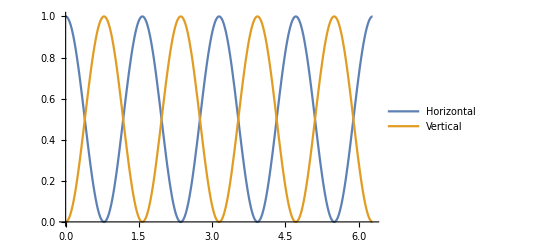

{{0,1,0,0},{1,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Clear[arbLP]
arbLP[θ_]:=MuellerRotation[θ].LPzero.Transpose[MuellerRotation[θ]];
horizontalResult=(arbLP[0].LR[θ,1/2].inc)[[1]][[1]]
verticalResult=(arbLP[π/2].LR[θ,1/2].inc)[[1]][[1]]

Plot[{horizontalResult,verticalResult},{θ,0,2π},PlotLegends->{"Horizontal","Vertical"}]
balancedIntensity=(LPzero.arbinc)[[1]]-(vertLP.arbinc)[[1]]
```

```mathematica
NonlinearModelFit[data,
```

### Looking at how the small angle approximation might be used to calculate the angle

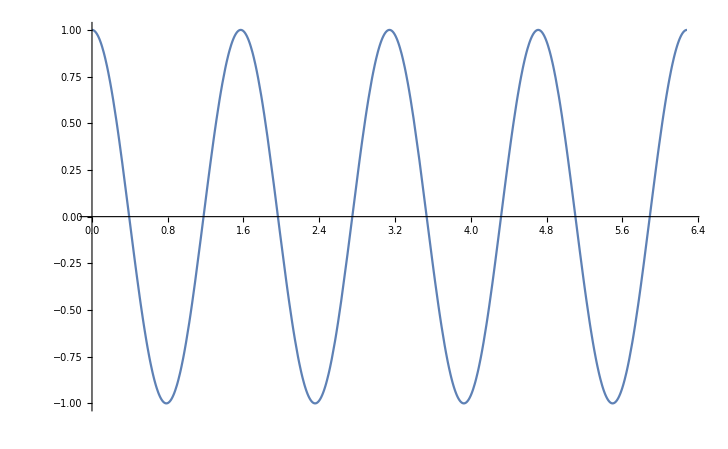

```mathematica
Plot[{balancedIntensity},{θ,0,2π}]
```

```mathematica
-100.241024-80.14339-60.089653-40.026209-2-0.050660-0.13962-0.236814-0.347976-0.419948-0.34255
```

```mathematica
2
```

2

```mathematica
Clear[newLR]
newLR[θ_,δ_]:=(MuellerRotation[θ].LRzero[δ].Transpose[MuellerRotation[θ]])
```

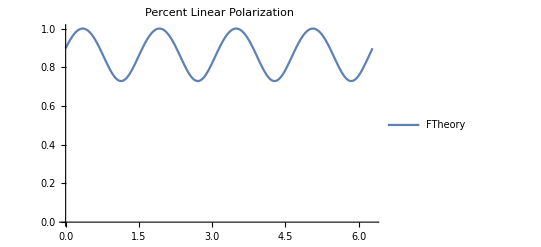

```mathematica
retardance=3.38;
shift795=42*π/180;
shift633=-20*π/180;
shift=shift633;
theory=Plot[Legended[Sqrt[(((LR[θ+shift,retardance].newLP.inc)[[2]])^2+((LR[θ+shift,retardance].newLP.inc)[[3]])^2)]/(LR[θ+shift,retardance].newLP.inc)[[1]],"FTheory"],{θ,0,2π},PlotRange->{0,Automatic},PlotLabel->"Percent Linear Polarization"]
```

```mathematica
Rasterize[Show[plot795,theory]]
```

-Graphics-

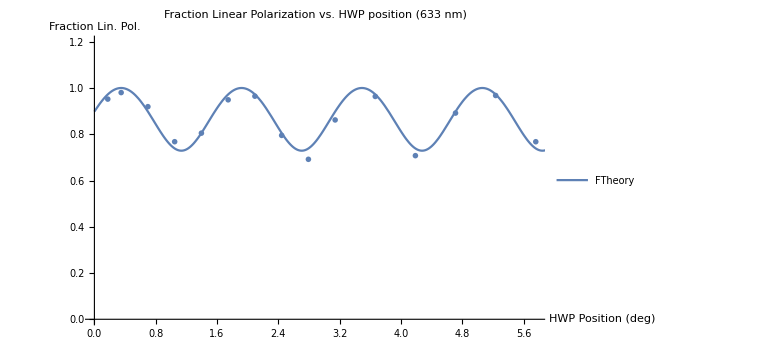

-Graphics-

```mathematica
Show[plot633,theory]
Rasterize[%]
```

1.5708

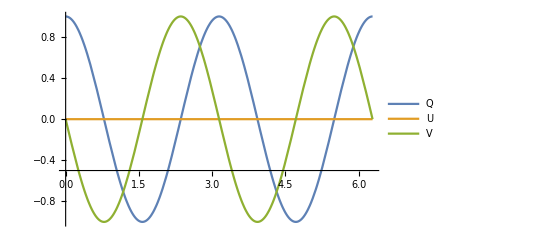

3.14159

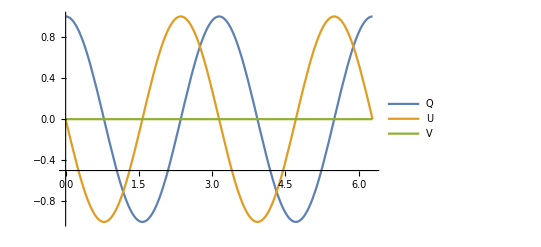

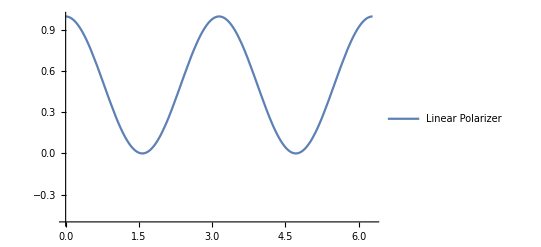

```mathematica
retard=.25*2*π
Plot[{Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[2]],"Q"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[3]],"U"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[4]],"V"]},{θ,0,2π},AxesOrigin->{0,-.5}]
retard=.5*2*π
Plot[{Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[2]],"Q"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[3]],"U"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[4]],"V"]},{θ,0,2π},AxesOrigin->{0,-.5}]
Plot[Legended[(LPzero.MuellerRotation[θ].inc)[[2]],"Linear Polarizer"],{θ,0,2π},AxesOrigin->{0,-.5}]
```